## More Riemann Sums

This Mathematica notebook is an extension of the work in the notebook RiemannSums.nb posted in the  of abstractmath.org.  It is produced by and is licensed under a  .  The work is discussed in the Gyre&Gimble post .

### Riemann Package (opened for modification)

This package provides PlotRiemann, which shows Riemann sum of a given integral with various choices of parameters, and CloudList, which plots the values of a number of random Riemann sums of the given integral.  It is a work in progress. You are encouraged to improve this work and to use it in your own publications and coursework.

```mathematica
SetOptions[Plot,AspectRatio->Automatic];
```

```mathematica
PlotBounded[expression_,range_,options___]:=Module[{g,f,left,right,newleft,newright,var,leftheight,rightheight,width,newrange},var=range[[1]];
f=Function[Release[var],expression];
left=range[[2]];
right=range[[3]];
width=right-left;
leftheight=f[left];
rightheight=f[right];
newleft=left-0.25*width;
newright=right+0.25*width;
newrange={var,newleft,newright};
g:=Plot[expression,Release[newrange],DisplayFunction->Identity,PlotStyle->{{RGBColor[0,0,1]}},options];
Show[g,Graphics[{Line[{{left,0},{left,leftheight}}],Line[{{right,0},{right,rightheight}}]}],DisplayFunction->$DisplayFunction]]
```

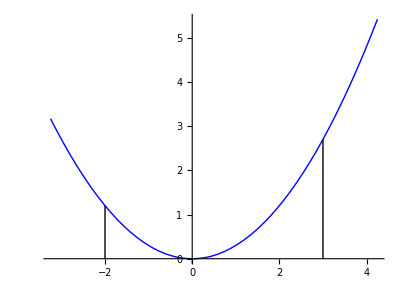

```mathematica
PlotBounded[.3x^2,{x,-2,3}]
```

```mathematica
RandomPartition[range_,mesh_]:=Module[{u=range[[2]],top=range[[3]],list={range[[2]]},v,newlist,actualmesh=0},While[u+mesh<top,v=u+Random[Real,mesh];
actualmesh=Max[actualmesh,v-u];
newlist:=Append[list,v];
u=v;
list=newlist];
partitionstring=StringJoin["Random partition with maximum norm ",ToString[mesh]];
actualmesh=Max[actualmesh,top-Last[list]];
Return[{Append[list,top],actualmesh}]]
```

```mathematica
rp1:=RandomPartition[{x,-2,3},.3]
```

```mathematica
rp1
```

{{-2,-1.97698,-1.83351,-1.81838,-1.75767,-1.50582,-1.30492,-1.29936,-1.15044,-0.917844,-0.687333,-0.44499,-0.400471,-0.125828,0.155328,0.25086,0.419736,0.513943,0.599295,0.820274,0.937626,1.18469,1.36397,1.42683,1.52482,1.74886,1.78467,1.8324,1.86968,2.14186,2.27678,2.31894,2.50731,2.5469,2.7513,3},0.281155}

```mathematica
Length[rp1[[1]]]
```

38

```mathematica
UniformPartition[range_,number_]:=Module[{bottom=range[[2]]//N,top=range[[3]]//N,actualmesh},actualmesh=(top-bottom)/number;
partitionstring=StringJoin["Uniform partition into ",ToString[number]," subintervals"];
Return[{N[Range[bottom,top,actualmesh]],actualmesh}]]
```

```mathematica
up1:=UniformPartition[{x,-2,3},5]
```

```mathematica
up1
```

{{-2.,-1.,0.,1.,2.,3.},1.}

```mathematica
Slices[expression_,variable_,list_,options___Rule]:=Module[{i=1,startlist=list,leftlist,rightlist,widthlist,selectlist,arealist,heightlist,valuelist,opt=Height/.{options}/.Options[RiemannData],f=Function[variable,expression]},leftlist=Drop[list,-1];
rightlist=Drop[list,1];
widthlist=rightlist-leftlist;
selectlist=Switch[opt,LeftSide,(heightstring="Left edge of subinterval used for height";leftlist),RightSide,(heightstring="Right edge of subinterval used for height";rightlist),Midpoint,(heightstring="Midpoint of subinterval used for height";
leftlist+0.5*widthlist),Random,(heightstring="Random point in subinterval used for height";
leftlist+(Random[Real,#]&/@widthlist))];
heightlist=f/@selectlist;
arealist=heightlist*widthlist;
{heightlist,arealist}]
```

```mathematica
(*Boxx::usage="Boxx[bottom, top, left, right]
produces a series of Line statements which in a
Graphics object will draw a hollow rectangle with
the corners given.  (Note that the built in
command Rectangle draws a solid rectangle.)"*)
```

```mathematica
Boxx[bottom_,top_,left_,right_]:=Line[{{left,bottom},{right,bottom},{right,top},{left,top},{left,bottom}}]
```

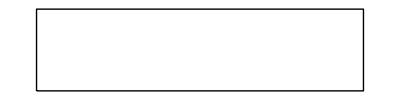

```mathematica
Show[Graphics[Boxx[0,.1,-.1,.3]]]
```

```mathematica
ShowSlices[partition_,heightlist_]:=Table[Boxx[0,heightlist[[i]],partition[[i]],partition[[i+1]]],{i,1,Length[partition]-1}]
```

```mathematica
Table[1+.1n,{n,0,Length[rp1[[1]]]}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2}

```mathematica
Options[RiemannData]:={Subintervals->12,Partition->Uniform,Mesh->intervallength/6.0,Height->Midpoint}
```

```mathematica
(*Options[PlotRiemann]:={FontSize->12}*)
```

```mathematica
RiemannData[expression_, range_, options___Rule] :=
	Block[{M=Mesh /. {options} 
			/. Options[RiemannData],
		S=Subintervals /. {options} 
			/. Options[RiemannData],
		P=Partition /. {options} 
			/. Options[RiemannData],
		variable=range[[1]],
		intervallength=range[[3]]-range[[2]]},
		list=Switch[P, Uniform, 
			UniformPartition[range, S],
			Random,
			RandomPartition[range, M]
           ]; 
	{list[[1]]} ~Join~ 
		Slices[expression, variable, list[[1]], options]
		~Join~ {list[[2]]}]
```

```mathematica
RiemannData[.3x^2,{x,-1,2},Subintervals->4]
```

{{-1.,-0.25,0.5,1.25,2.},{0.117188,0.0046875,0.229688,0.792187},{0.0878906,0.00351562,0.172266,0.594141},0.75}

```mathematica
RiemannData[.3x^2,{x,-1,2},Partition->Uniform,Height->RightSide,Subintervals->4]
```

{{-1.,-0.25,0.5,1.25,2.},{0.01875,0.075,0.46875,1.2},{0.0140625,0.05625,0.351563,0.9},0.75}

```mathematica
RiemannSum[expression_,range_,options___Rule]:=Apply[Plus,RiemannData[expression,range,options][[3]]]
```

```mathematica
RiemannSum[.3x^2,{x,-1,2},Subintervals->4]
```

0.857813

```mathematica
RiemannSum[.3x^2,{x,-1,2},Subintervals->4]
```

0.857813

```mathematica
PlotRiemann[expression_,range_]:=PlotRiemann[expression,range,{},{}];
PlotRiemann[expression_,range_,{plotoptions___},{riemannoptions___}]:=Block[{g,u,partition,heightlist,sum,mesh,integralvalue,outstring},(u=RiemannData[expression,range,riemannoptions];
partition=u[[1]];
heightlist=u[[2]];
sum=Apply[Plus,u[[3]]];
mesh=u[[4]];
integralvalue=NIntegrate[expression,range];
outstring=StringJoin["\n",partitionstring,"\n",heightstring,"\n","Norm = ",ToString[mesh],"\n","Riemann Sum = ",ToString[Chop[sum]],"\n","Definite Integral = ",ToString[integralvalue]];
g:=Plot[expression,range,DisplayFunction->Identity,PlotLabel->outstring,PlotStyle->{{RGBColor[0,0,1]}},plotoptions];
h:=Graphics[{RGBColor[.8,.3,0],ShowSlices[partition,heightlist]}];
Show[g,h,DisplayFunction->$DisplayFunction])]
```

```mathematica
Manipulate[PlotRiemann[Sqrt[4-x^2],{x,0,2},{ImageSize->{350,350}},
{Partition -> Uniform,Height -> Midpoint,Subintervals ->n}],{{n,12},1,200,1},SaveDefinitions->True]
```

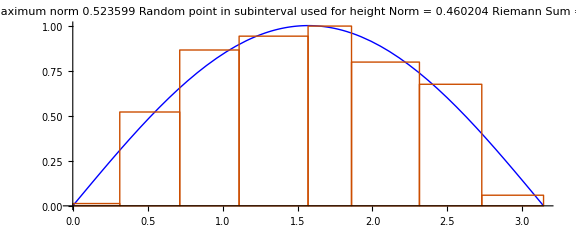

```mathematica
PlotRiemann[Sin[x],{x,0,Pi},{ImageSize->Large},
{Partition -> Random,Height -> Random}]
```

### CloudList

```mathematica
(*CloudList{e, i,n] produces n points(m, riemann sum of expression e on the interval i), where the Riemann Sum has random mesh m with random choice of points in each subinterval.*)
```

```mathematica
Remove[CloudList]
```

```mathematica
CloudList[expression_,range_,n_]:=Module[{l={},s,mesh,a,b,u},a=range[[2]];b=range[[3]];
Do[(mesh=Random[Real,{0,(b-a)/5}];
u=RiemannData[expression,range,Partition->Random,Mesh->mesh,Height->Random];
s=Apply[Plus,u[[3]]];
l=Append[l,{u[[4]],s}]),{i,1,n}];
l]
```

```mathematica
CloudList[Sin[x],{x,0,Pi},8]
```

{{0.535241,2.01293},{0.0314288,1.99904},{0.120394,2.00131},{0.362252,1.98771},{0.238768,1.98746},{0.222597,1.98345},{0.553144,1.95101},{0.108952,1.99559}}

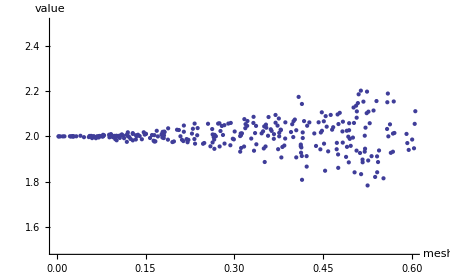

```mathematica
ListPlot[CloudList[Sin[x],{x,0,Pi},300],ImageSize->{450,450},AxesOrigin->{0,0},AxesLabel->{"mesh","value"},PlotRange->{{0,.6},{1.5,2.5}},PlotRangeClipping->True]
```

### MidpointCloudList

```mathematica
(* This produces a cloud of midpoint Riemann sums with random mesh.*)
```

```mathematica
Remove[MidpointCloudList]
```

```mathematica
CloudList[expression_,range_,n_]:=Module[{l={},s,mesh,a,b,u},a=range[[2]];b=range[[3]];
Do[(mesh=Random[Real,{0,(b-a)}];
u=RiemannData[expression,range,Partition->Random,Mesh->mesh,Height->Random];
s=Apply[Plus,u[[3]]];
l=Append[l,{u[[4]],s}]),{i,1,n}];
l]
```

```mathematica
MidpointCloudList[expression_, range_, n_] := Module[{l = {}, s, mesh, a, b, u}, a = range[[2]]; b = range[[3]];
  Do[(mesh=Random[Real,{0,(b-a)}];
    u = RiemannData[expression, range, Partition -> Random, Mesh->mesh, Height -> Midpoint]; 
    s = Apply[Plus, u[[3]]];
    l = Append[l, {u[[4]], s}]), {i, 1, n}];
  l]
```

```mathematica
Random[Integer,{1,100}]
```

2

```mathematica
MidpointCloudList[Sin[x],{x,0,Pi},3]
```

{{1.69562,2.22813},{2.02096,2.30749},{0.444378,2.00986}}

```mathematica
MidpointCloudList[Sqrt[4-x^2],{x,0,2},3]
```

{{1.07808,3.25389},{0.600178,3.18064},{1.21955,3.28437}}

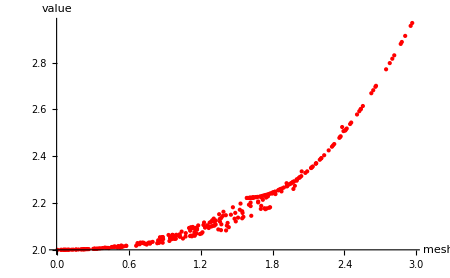

```mathematica
ListPlot[MidpointCloudList[Sin[x],{x,0,Pi},300],PlotStyle->Red,ImageSize->{450,450},AxesLabel->{"mesh","value"}]
```

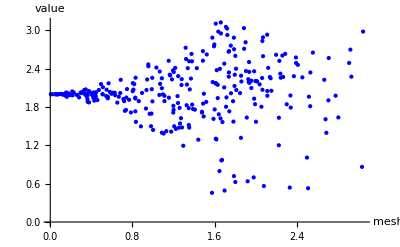

```mathematica
ListPlot[CloudList[Sin[x],{x,0,Pi},300],PlotStyle->Blue,AxesLabel->{"mesh","value"}]
```

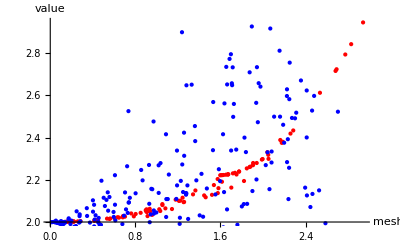

```mathematica
Show[Graphics[ListPlot[MidpointCloudList[Sin[x],{x,0,Pi},100],PlotStyle->Red,AxesLabel->{"mesh","value"}]],ListPlot[CloudList[Sin[x],{x,0,Pi},300],PlotStyle->Blue,AxesLabel->{"mesh","value"}]]
```

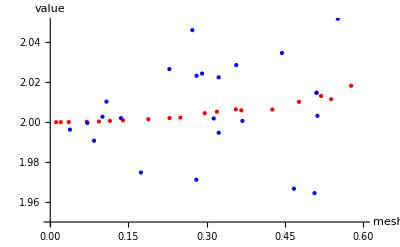

```mathematica
ListPlot[{MidpointCloudList[Sin[x],{x,0,Pi},100],CloudList[Sin[x],{x,0,Pi},100]},PlotStyle->{Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.6},{1.95,2.05}},PlotRangeClipping->True]
```

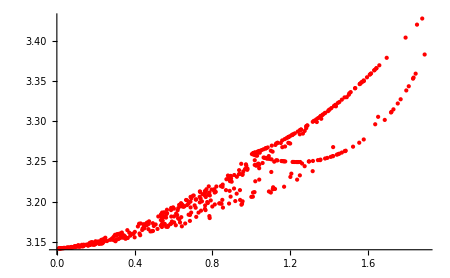

```mathematica
ListPlot[MidpointCloudList[Sqrt[4-x^2],{x,0,2},500],PlotStyle->Red,ImageSize->{450,450}]
```

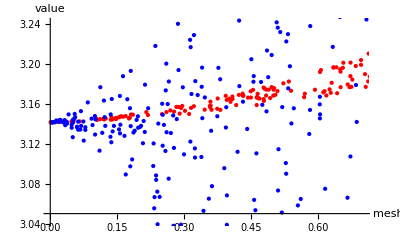

```mathematica
ListPlot[{MidpointCloudList[Sqrt[4-x^2],{x,0,2},300],CloudList[Sqrt[4-x^2],{x,0,2},600]},PlotStyle->{Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.7},{Pi-.1,Pi+.1}},PlotRangeClipping->False]
```

### Uniform

```mathematica
(* This produces uniform-subinterval Riemann Sums with number of subintervals = 1,2,...,n.  There are versions for leftside height,midpoint height and rightside height.  These need to be consolidated into one command with options.*)
```

```mathematica
UniformMidpointCloudList[expression_, range_, n_] := Table[{(range[[3]]-range[[2]])/i,RiemannSum[expression,range,Partition->Uniform,Subintervals->i]},{i,n}]
```

```mathematica
UniformMidpointCloudList[Sqrt[4-x^2],{x,0,2},5]
```

{{2,3.4641},{1,3.25937},{2/3,3.20641},{1/2,3.18393},{2/5,3.17199}}

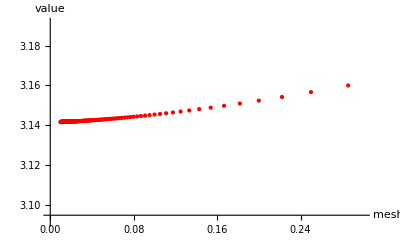

```mathematica
ListPlot[UniformMidpointCloudList[Sqrt[4-x^2],{x,0,2},200],PlotStyle->Red,AxesLabel->{"mesh","value"},PlotRange->{{0,.3},{Pi-.05,Pi+.05}},PlotRangeClipping->False]
```

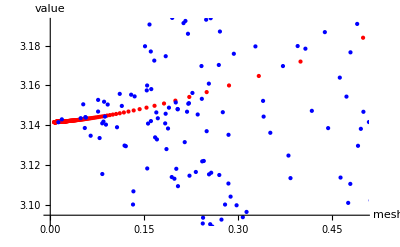

```mathematica
ListPlot[{UniformMidpointCloudList[Sqrt[4-x^2],{x,0,2},300],CloudList[Sqrt[4-x^2],{x,0,2},600]},PlotStyle->{Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.5},{Pi-.05,Pi+.05}},PlotRangeClipping->False]
```

```mathematica
UniformLeftSideCloudList[expression_, range_, n_] := Table[{(range[[3]]-range[[2]])/i,RiemannSum[expression,range,Height -> LeftSide,Partition->Uniform,Subintervals->i]},{i,n}]
```

```mathematica
UniformLeftSideCloudList[Sqrt[4-x^2],{x,0,2},5]
```

{{2,4.},{1,3.73205},{2/3,3.58422},{1/2,3.49571},{2/5,3.43705}}

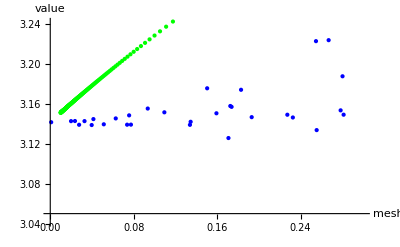

```mathematica
ListPlot[{UniformLeftSideCloudList[Sqrt[4-x^2],{x,0,2},200],CloudList[Sqrt[4-x^2],{x,0,2},200]},PlotStyle->{Green,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.3},{Pi-.1,Pi+.1}},PlotRangeClipping->False]
```

```mathematica
UniformRightSideCloudList[expression_, range_, n_] := Table[{(range[[3]]-range[[2]])/i,RiemannSum[expression,range,Height -> RightSide,Partition->Uniform,Subintervals->i]},{i,n}]
```

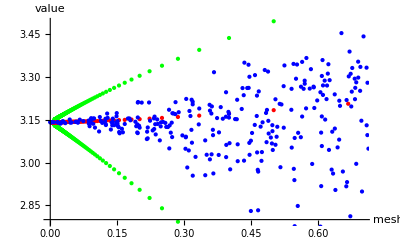

```mathematica
ListPlot[{UniformLeftSideCloudList[Sqrt[4-x^2],{x,0,2},200],UniformRightSideCloudList[Sqrt[4-x^2],{x,0,2},200],UniformMidpointCloudList[Sqrt[4-x^2],{x,0,2},400],CloudList[Sqrt[4-x^2],{x,0,2},700]},PlotStyle->{Green,Green,Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.7},{Pi-.35,Pi+.35}},PlotRangeClipping->False]
```

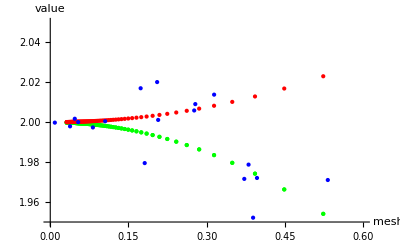

```mathematica
ListPlot[{UniformLeftSideCloudList[Sin[x],{x,0,Pi},100],UniformRightSideCloudList[Sin[x],{x,0,Pi},100],UniformMidpointCloudList[Sin[x],{x,0,Pi},100],CloudList[Sin[x],{x,0,Pi},100]},PlotStyle->{Green,Green,Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.6},{1.95,2.05}},PlotRangeClipping->False]
```

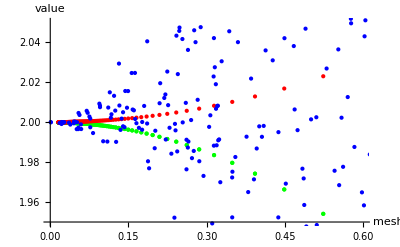

```mathematica
ListPlot[{UniformLeftSideCloudList[Sin[x],{x,0,Pi},200],UniformRightSideCloudList[Sin[x],{x,0,Pi},200],UniformMidpointCloudList[Sin[x],{x,0,Pi},200],CloudList[Sin[x],{x,0,Pi},1000]},PlotStyle->{Green,Green,Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{{0,.6},{1.95,2.05}},PlotRangeClipping->False]
```

```mathematica
ManyList[expression_,range_,n_,meshrange_,valuerange_]:=ListPlot[{UniformLeftSideCloudList[expression,range,n],UniformRightSideCloudList[expression,range,n],UniformMidpointCloudList[expression,range,n],CloudList[expression,range,4n]},PlotStyle->{Green,Green,Red,Blue},AxesLabel->{"mesh","value"},PlotRange->{meshrange,valuerange},PlotRangeClipping->False]
```

```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

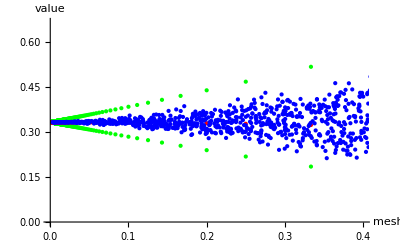

```mathematica
ManyList[x^2,{x,0,1},400,{0,.4},{0,2/3}]
```

```mathematica
Integrate[x^2,{x,0,2}]
```

8/3

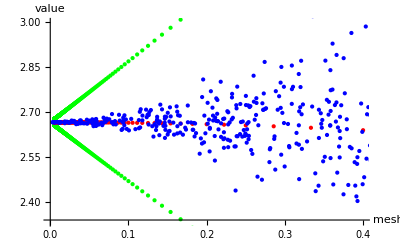

```mathematica
ManyList[x^2,{x,0,2},400,{0,.4},{7/3,3}]
```

```mathematica
Integrate[x^(3/2),{x,0,2}]//N
```

2.26274

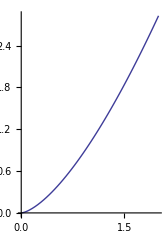

```mathematica
Plot[x^(3/2),{x,0,2}]
```

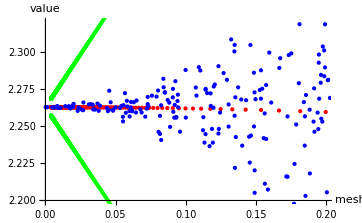

```mathematica
ManyList[x^(3/2),{x,0,2},500,{0,.2},{2.2,2.32}]
```

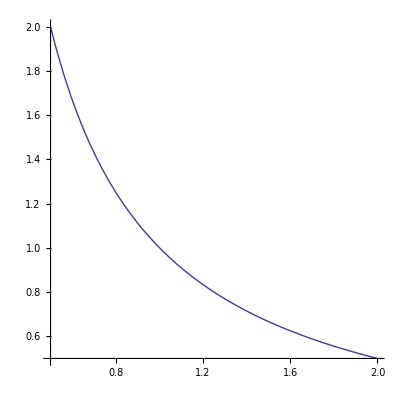

```mathematica
Plot[1/x,{x,1/2,2}]
```

```mathematica
Integrate[1/x,{x,1/2,2}]//N
```

1.38629

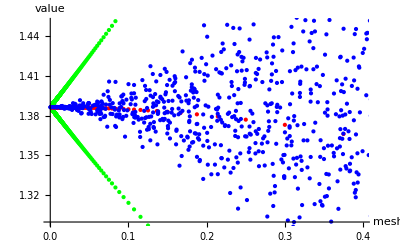

```mathematica
ManyList[1/x,{x,1/2,2},500,{0,.4},{1.3,1.45}]
```